{ErrorBar[0.1,0.5],ErrorBar[0.1,0.5],ErrorBar[0.1,0.5],ErrorBar[0.1,0.5],ErrorBar[0.1,0.5],ErrorBar[0.1,0.5],ErrorBar[0.1,0.5]}

{{{294.8,22.5},ErrorBar[0.1,0.5]},{{298.7,25},ErrorBar[0.1,0.5]},{{304,28},ErrorBar[0.1,0.5]},{{308.8,30.5},ErrorBar[0.1,0.5]},{{313.8,34.5},ErrorBar[0.1,0.5]},{{318,37.5},ErrorBar[0.1,0.5]},{{323,41},ErrorBar[0.1,0.5]}}

-170.585+0.653877 T

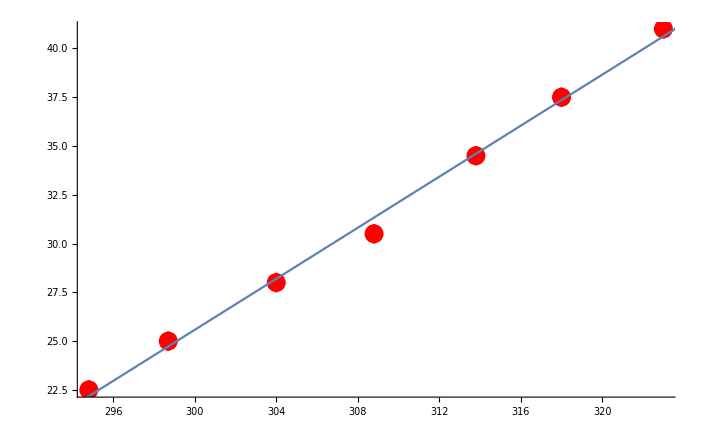

```mathematica
Needs["ErrorBarPlots`"]
data={{294.8,22.5},{298.7,25},{304,28},{308.8,30.5},{313.8,34.5},{318,37.5},{323,41}};
error = ConstantArray[ErrorBar[0.1,0.5],Length[data]]
withError= Transpose[{data,error}]
P = Fit[data,{1,T},T]
Show[ErrorListPlot[withError,PlotStyle->Red ],Plot[P,{T,294,325}]]
```

```mathematica
Show[%128,AxesLabel->{HoldForm["T (K)"],HoldForm["P (bar)"]},PlotLabel->HoldForm[Graph de Psat en fonction de " T"],LabelStyle->{GrayLevel[0]}]
```

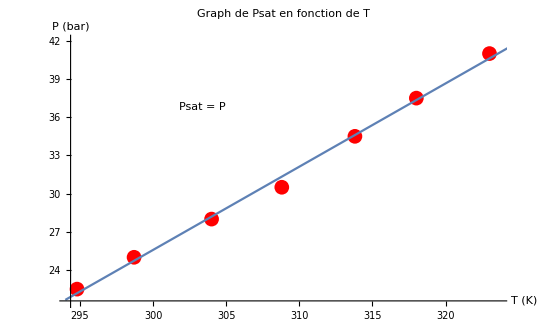

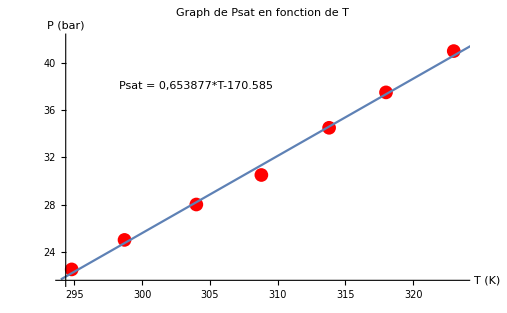

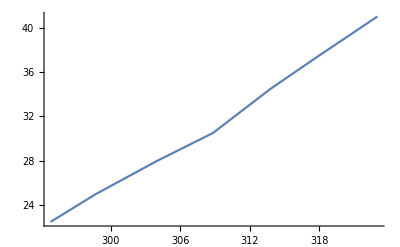

```mathematica
Get["D:\\COURS\\Wolfram\\incertitudes.m"]
```

```mathematica
uncertitude[3X+2Y/Z,{X,Y,Z}]
```

√(9 U_X^2+(4 (Z^2 U_Y^2+Y^2 U_Z^2))/Z^4)

```mathematica
f := Function[{X,Y,Z},uncertitude[3X+2Y/Z, {X,Y,Z}]]
```

```mathematica
f
```

Function[{X,Y,Z},uncertitude[3 X+(2 Y)/Z,{X,Y,Z}]]

```mathematica
f[X,Y,Z]
f[1,2,3]
```

√(9 U_X^2+(4 (Z^2 U_Y^2+Y^2 U_Z^2))/Z^4)

0

```mathematica
f = getFunction[n*R*T/V,{T,V}]
```

Function[{T,V},uncertitude[(n R T)/V,{T,V}]]

```mathematica
f
```

Function[{T,V},uncertitude[(n R T)/V,{T,V}]]

```mathematica
abcd[yolo_]:=yolo*2;
```

```mathematica
abcd
```

abcd

```mathematica
Information[abcd]
```

Global`abcd

abcd[yolo_]:=yolo 2

```mathematica
Information[f]
```

Global`f

f=Function[{T,V},uncertitude[(n R T)/V,{T,V}]]

```mathematica
clearAll[P]
```

clearAll[-170.585+0.653877 T]

```mathematica
Clear[P]
```

```mathematica
f= getFunction[P*V,{P,V}]
```

Function[Join[{P,V},Table[U_({P,V}⟦n⟧),{n,1,Length[{P,V}]}]],uncertitude[P V,{P,V}]]

```mathematica
f[0.2,26.5,0.05,0.5]
```

Function[Join[{P,V},Table[U_({P,V}⟦n⟧),{n,1,Length[{P,V}]}]],uncertitude[P V,{P,V}]][0.2,26.5,0.05,0.5]

```mathematica
uncertitude[P*V,{P,V}]
```

√(V^2 U_P^2+P^2 U_V^2)

```mathematica
Function[{ΔT}, ΔT*5][5]
```

25

```mathematica
ΔT
```

ΔT

$Failed